```mathematica
energy[x_, y_] = (x^2 -1)^2 + ((y - x)^2 - 1)^2
force[x_, y_] = -D[energy[a, b],{{a, b}}]/.{a->x, b->y}
```

(-1+x^2)^2+(-1+(-x+y)^2)^2

{-4 x (-1+x^2)+4 (-x+y) (-1+(-x+y)^2),-4 (-x+y) (-1+(-x+y)^2)}

```mathematica
sol = NDSolve[{x''[t] == force[x[t], y[t]][[1]],y''[t] == force[x[t], y[t]][[2]] , x[0] == 2, x'[0] == 0, y[0] == 4, y'[0] == 0}, {x[t], y[t]}, {t, 0, 100}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

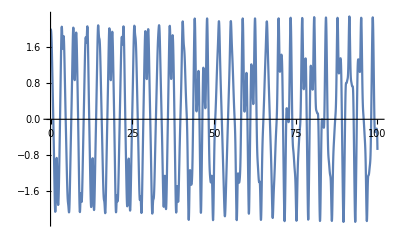

```mathematica
Plot[x[t]/. sol, {t, 0, 100}]
```

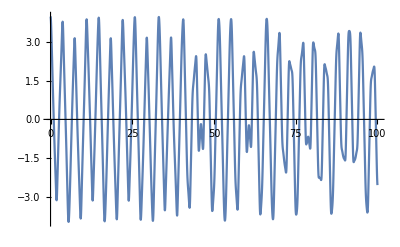

```mathematica
Plot[y[t]/. sol, {t, 0, 100}]
```

```mathematica
vis[s_]:=Point[{{0,0},{(x[t]/.sol[[1]])/.t->s,0},{(y[t]/.sol[[1]])/.t->s,0}}]
```

```mathematica
Animate[Graphics[vis[s],PlotRange->{{-10,10},{-0.1,0.1}}],{s,0,100}]
```

```mathematica
Graphics[vis[0]]
```

-Graphics-

```mathematica
hessian[x_, y_] = D[energy[a, b], {{a, b}, 2}] /.{a->x, b->y}
```

{{8 x^2+4 (-1+x^2)+8 (-x+y)^2+4 (-1+(-x+y)^2),-8 (-x+y)^2-4 (-1+(-x+y)^2)},{-8 (-x+y)^2-4 (-1+(-x+y)^2),8 (-x+y)^2+4 (-1+(-x+y)^2)}}

```mathematica
evec[x_, y_] =Eigenvectors[hessian[x, y]]
eval[x_, y_] = Eigenvalues[hessian[x, y]]
```

{{-(-1+3 x^2-√(5-30 x^2+45 x^4+48 x y-144 x^3 y-24 y^2+216 x^2 y^2-144 x y^3+36 y^4))/(2 (-1+3 x^2-6 x y+3 y^2)),1},{-(-1+3 x^2+√(5-30 x^2+45 x^4+48 x y-144 x^3 y-24 y^2+216 x^2 y^2-144 x y^3+36 y^4))/(2 (-1+3 x^2-6 x y+3 y^2)),1}}

{2 (-3+9 x^2-12 x y+6 y^2-√(5-30 x^2+45 x^4+48 x y-144 x^3 y-24 y^2+216 x^2 y^2-144 x y^3+36 y^4)),2 (-3+9 x^2-12 x y+6 y^2+√(5-30 x^2+45 x^4+48 x y-144 x^3 y-24 y^2+216 x^2 y^2-144 x y^3+36 y^4))}

```mathematica
Norm[evec[0.5, 0.6][[1]]]
```

1.51429

```mathematica
vec[x_, y_] = Normalize[evec[x, y][[1]]]
```

{-(-1+3 x^2-√(5-30 x^2+45 x^4+48 x y-144 x^3 y-24 y^2+216 x^2 y^2-144 x y^3+36 y^4))/(2 (-1+3 x^2-6 x y+3 y^2) √(1+1/4 Abs[(-1+3 x^2-√(5-30 x^2+45 x^4+48 x y-144 x^3 y-24 y^2+216 x^2 y^2-144 x y^3+36 y^4))/(-1+3 x^2-6 x y+3 y^2)]^2)),1/(√(1+1/4 Abs[(-1+3 x^2-√(5-30 x^2+45 x^4+48 x y-144 x^3 y-24 y^2+216 x^2 y^2-144 x y^3+36 y^4))/(-1+3 x^2-6 x y+3 y^2)]^2))}

```mathematica
Norm[vec[0.5, 0.7]]
```

1.

```mathematica
alpha0[s_] =vec[(x[t]/.sol[[1]])/.t->s, (y[t]/.sol[[1]])/.t->s].{(x[t]/.sol[[1]])/.t->s, (y[t]/.sol[[1]])/.t->s};
```

```mathematica
alpha0[0.3]
```

3.61278

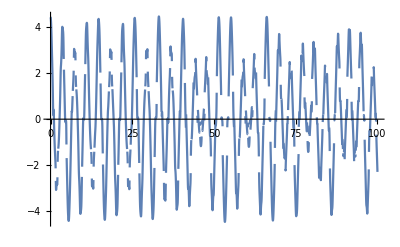

```mathematica
Plot[alpha0[s], {s, 0, 100}]
```